# Min number of patients

```mathematica
MeanNonResponseVolumeChange=20;
StandardDeviationOfVolumeChange=30;
GroupOfResponses[samplesize_,treatmenteffect_]:=RandomVariate[NormalDistribution[MeanNonResponseVolumeChange+treatmenteffect,StandardDeviationOfVolumeChange],samplesize]
```

```mathematica
ManyNonResponders=GroupOfResponses[200,0];
```

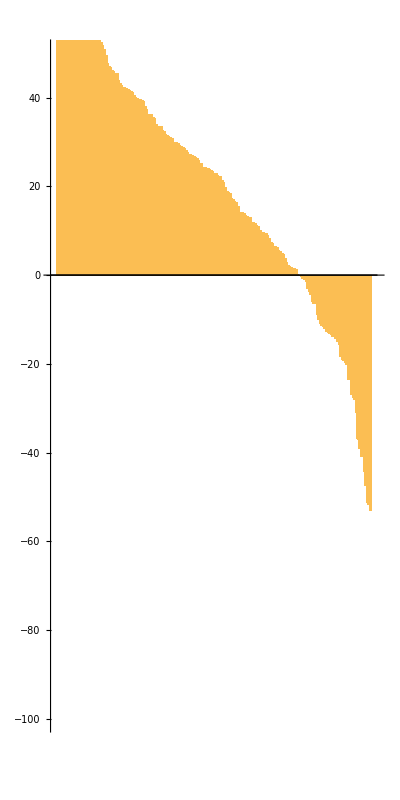

```mathematica
BarChart[Reverse[Sort[ManyNonResponders]],PlotRange->{-100,50},AspectRatio->2,ImageSize->{{250},{250}}]
```

```mathematica
(* treatment effect of '0' corresponds to 5% rate of Objective Response *)
ManyNonResponders=GroupOfResponses[100000,0];
Length[Select[ManyNonResponders,#<-30&]]/Length[ManyNonResponders]//N
```

0.04751

```mathematica
(* 30% rate of Objective Response (volume change below -30%) with treatment effect of -34 *)
ManyResponders=GroupOfResponses[100000,-34];
Length[Select[ManyResponders,#<-30&]]/Length[ManyResponders]//N
ManyResponders=GroupOfResponses[200,-34];
```

0.29566

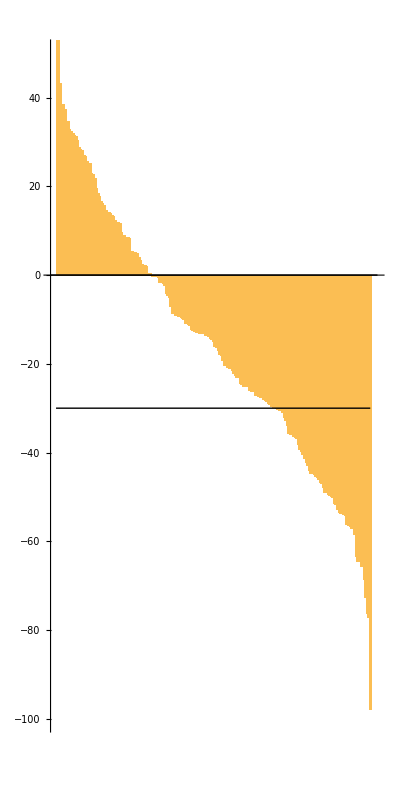

```mathematica
BarChart[Reverse[Sort[ManyResponders]],PlotRange->{-100,50},AspectRatio->2,Epilog->{Black,Line[{{0,-30},{200,-30}}]}]
```

```mathematica
(* Simon Two Stage Design population sizes with 80% Power, 10% type 1 error rate (one-sided), response rate for bad drug p0 = 10%, response rate for good drug p1 = 30%*)
Nstage1=7;
Nstage2=18;

(* number of responses required *)
ResponsesStage1=1;
ResponsesStage2=4;
```

```mathematica
TotalNumberOfTumorSubtypes=10;
NumberOfResponsiveSubtypes=1;
NumberOfNonResponsiveSubtypes=TotalNumberOfTumorSubtypes-NumberOfResponsiveSubtypes;
```

## Min num of patients assessment

```mathematica
Stage1ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage1,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage1,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage1Assessment[listofvolumes_]:=
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]
```

```mathematica
Map[SimonStage1Assessment,Stage1ResponsesInGroups[-40]]
```

{1,0,0,1,0,0,1,0,0,0}

```mathematica
ManySimonStage1Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage1Assessment,Stage1ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage1Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage1Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;

{TrialsThatShouldBePositive}
]
```

```mathematica
sims=1000;
SimonStage1PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage1Power[sims,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

```mathematica
Dimensions[SimonStage1PowerAndErrorRateVSEffect]
```

{61,1001}

```mathematica
AveResponses=Map[Mean,SimonStage1PowerAndErrorRateVSEffect[[All,Range[2,sims]]]];
```

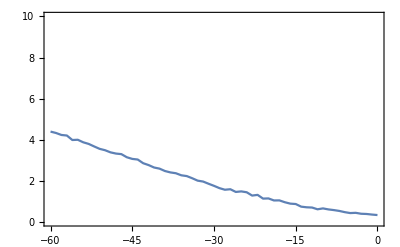

```mathematica
ListPlot[
{
Transpose[{SimonStage1PowerAndErrorRateVSEffect⟦All,1⟧, AveResponses}]

},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,10}]
```

```mathematica
Mean[SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧⟦All,2⟧]//N
```

2.21311

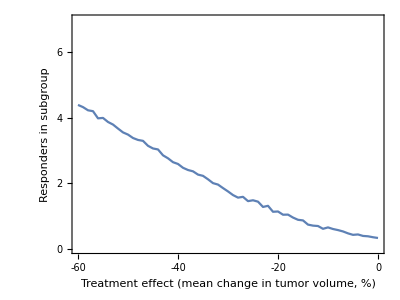

```mathematica
ListPlot[
{
Transpose[{SimonStage1PowerAndErrorRateVSEffect⟦All,1⟧, AveResponses}]

},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-60,0},{0,7}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,i,{0.02,0}},{i,0,7,1}],None},{Table[{i,i,{0.02,0}},{i,-60,0,10}],None}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Responders in subgroup"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}}]
```

```mathematica
Export[NotebookDirectory[]<>"Number of responses by treatment effect, Stage 1.pdf",%,"PDF"]
```

Export::noopen: Cannot open C:\Users\Deborah\Dropbox (HMS)\Palmer, 2016\Basket trials submission\Revision\revision code\Minimum number of patients\Number of responses by treatment effect, Stage 1.pdf.

$Failed

## Simon stage 2 assessment

```mathematica
Stage2ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage2,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage2,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage2Assessment[listofvolumes_]:=
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]
```

```mathematica
Map[SimonStage2Assessment,Stage2ResponsesInGroups[-40]]
```

{4,0,4,1,1,0,1,0,0,1}

```mathematica
ManySimonStage2Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage2Assessment,Stage2ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage2Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage2Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;


{TrialsThatShouldBePositive}
]
```

```mathematica
sims=1000
```

1000

```mathematica
SimonStage2PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage2Power[sims,treatmenteffect]}],{treatmenteffect,-60,0,1}];
AveResponses=Map[Mean,SimonStage2PowerAndErrorRateVSEffect[[All,Range[2,sims]]]];
```

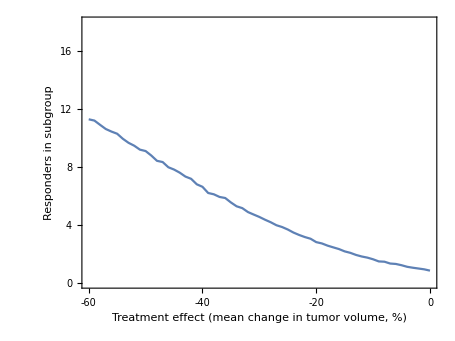

```mathematica
ListPlot[
{
Transpose[{SimonStage2PowerAndErrorRateVSEffect⟦All,1⟧, AveResponses}]
},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-60,0},{0,18}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,i,{0.02,0}},{i,0,18,2}],None},{Table[{i,i,{0.02,0}},{i,-60,0,10}],None}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Responders in subgroup"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}}]
```

```mathematica
Export[NotebookDirectory[]<>"Number of responses by treatment effect, Stage 2.pdf",%,"PDF"]
```

C:\Users\Deborah\Dropbox (HMS)\Palmer, 2016\Basket trials submission\Revision\revision code\Minimum number of patients\Number of responses by treatment effect, Stage 2.pdf